# 19: Least Squares Stability

## A Familiar Example: Polynomial Fitting

We are going to fit 100 equally spaced data points on [0,1] using a degree 14 polynomial.

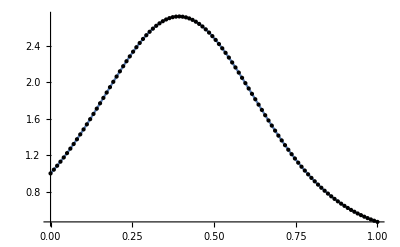

```mathematica
{m,n}={100,15};{a,b}={0.0,1.0};
f[t_]:=Exp[Sin[4t]]
ts=Range[a,b,(b-a)/(m-1)];bs=f[ts];
Plot[ f[x],{x,a,b},Epilog->Point[{ts,bs}ᵀ]]
```

We build the least square matrix. We already have the RHS. The built-in least squares solver has no problem.

```mathematica
Clear[fs,t]
fs[t_]=Table[ t^(i-1),{i,n}];
A=Map[fs,ts];
xBuiltIn=LeastSquares[A,ys]
yBuiltIn=A.xBuiltIn;
```

{1.00001,3.99348,8.45434,-12.5163,149.202,-1642.39,8801.38,-32945.5,85181.4,-147581.,170033.,-128654.,61470.2,-16819.7,2006.79}

In contrast, a simple normal equation version does.

```mathematica
xNormalEq = LinearSolve[Aᵀ.A,Aᵀ.ys]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{100.,50.,33.5017,25.2525,20.3034,17.0042,14.6479,12.8809,11.5067,10.4076,«5»},«9»,«5»} may contain significant numerical errors.

{0.999939,4.01889,7.05864,18.4902,-217.689,996.982,-3636.01,7174.4,-5612.21,-2051.96,5619.52,-612.789,-3949.8,2917.74,-658.283}

You might wonder (briefly I hope) which is better

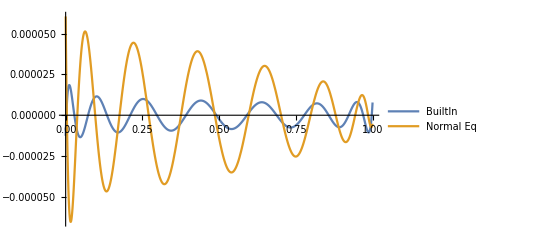

```mathematica
BuiltInPoly[t_]:=xBuiltIn.fs[t]
NormalEqPoly[t_]:=xNormalEq.fs[t]
Plot[{f[t]-BuiltInPoly[t],f[t]-NormalEqPoly[t]},{t,a,b},
PlotLegends->{"BuiltIn","Normal Eq"}]
```

The explanation is actually pretty simple. In the normal equations we built and used a “bad” matrix. The plan for today is to look at this a bit more closely.

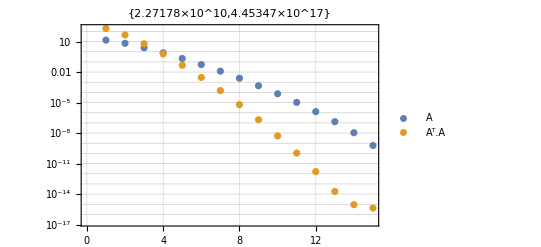

```mathematica
σsA=SingularValueList[A,Tolerance->0];σsAtA=SingularValueList[Aᵀ.A,Tolerance->0];
ListLogPlot[ {σsA,σsAtA},
Frame->True,PlotLegends->{"A","Aᵀ.A"},
PlotLabel->{σsA⟦1⟧/σsA⟦-1⟧,σsAtA⟦1⟧/σsAtA⟦-1⟧},
GridLines->{Automatic,Table[1.0 10^i,{i,-16,5}]}]
```

So how should we think about this:

10^10 is big. 10^17 is huge and triggers the linear solve warnings!

The basis fs[t]={1,t,t^2,…,t^14} we used to build our matrix A is a lousy “almost parallel” basis! The angle between vectors is tiny:

fs[0.1]={1,0.1,0.01,0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10,1.×10^-11,1.×10^-12,1.×10^-13,1.×10^-14}

fs[0.05]={1,0.05,0.0025,0.000125,6.25×10^-6,3.125×10^-7,1.5625×10^-8,7.8125×10^-10,3.90625×10^-11,1.95313×10^-12,9.76563×10^-14,4.88281×10^-15,2.44141×10^-16,1.2207×10^-17,6.10352×10^-19}

```mathematica
ArcCos[(fs[0.1]/Norm[fs[0.1]]).(fs[0.05]/Norm[fs[0.05]])]
```

0.0502724

A simple solution would be to use a better basis. As an example, the trig polynomials are a better basis! The other option is to just be very careful with the bad matrix A we have been given.   Our targets (the best we can expect to get) are given by the sensitivities from the previous lecture

```mathematica
Options[SingularValueList]
```

{Cubics→False,Method→Automatic,Quartics→False,Tolerance→Automatic}

```mathematica
{σ1,σn}=SingularValueList[A,Tolerance->0]⟦{1,-1}⟧;
xBuiltIn=LeastSquares[A,bs]; yBuiltIn=A.xBuiltIn;
{k,θ,η}={σ1/σn,ArcCos[Norm[yBuiltIn]/Norm[bs]],(Norm[A,2]*Norm[xBuiltIn])/Norm[A.xBuiltIn]}
TableForm[({{1/Cos[θ], k/(η Cos[θ])}, {k/Cos[θ], k+(k^2*Tan[θ])/η}}),
TableHeadings->{{"b","A"},{"y","x"}}]
```

{2.27178×10^10,4.86894×10^-6,210356.}

| y | x
b | 1. | 107997.
A | 2.27178×10^10 | 3.46635×10^10

Lets see how our different algorithms do!

### QRDecomposition

First our gold-standard algorithm

```mathematica
{Q,R}=QRDecomposition[A]; Q=Qᵀ;
xQR=LinearSolve[R,Qᵀ.bs];xBuiltIn;
(xQR-xBuiltIn)/xBuiltIn
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-10.,-5.,-3.35017,-2.52525,-2.03034,-1.70042,-1.46479,-1.28809,-1.15067,-1.04076,«5»},«9»,«5»} may contain significant numerical errors.

{7.69286×10^-12,1.07367×10^-12,2.52529×10^-11,1.32605×10^-10,2.77243×10^-11,4.14961×10^-12,2.53193×10^-12,2.64113×10^-12,2.73984×10^-12,2.86738×10^-12,3.10564×10^-12,3.48806×10^-12,4.04408×10^-12,4.81878×10^-12,5.87303×10^-12}

That is just about how we expected it to do! Remember QR is backward stable but the condition number of A is big!

The errors in Mathematica are smaller than those reported in the text for matlab.

### Augmented QRDecomposition

We do not need the if we augment A with b.  This trick makes the computation worse! Apparently it has little effect in matlab. It would be faster in Julia!

```mathematica
APlus=ArrayFlatten[{{A,{bs}ᵀ}}];
RPlus=QRDecomposition[APlus]⟦2⟧;
R=RPlus⟦1;;n,1;;n⟧; RHS=RPlus⟦1;;n,n+1⟧;
xQRPlus=LinearSolve[R,RHS];xBuiltIn;
(xQRPlus-xBuiltIn)/xBuiltIn
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-10.,-5.,-3.35017,-2.52525,-2.03034,-1.70042,-1.46479,-1.28809,-1.15067,-1.04076,«5»},«9»,«5»} may contain significant numerical errors.

{-8.83349×10^-12,-5.59065×10^-10,1.42369×10^-8,1.9862×10^-7,1.86734×10^-7,1.1775×10^-7,1.01389×10^-7,8.65292×10^-8,7.56533×10^-8,7.03722×10^-8,6.97332×10^-8,7.28154×10^-8,7.92431×10^-8,8.91476×10^-8,1.03153×10^-7}

These errors are the same as reported for matlab in the text!

## Theorem 19.1

Least Squares computed using Householder QR (for a full rank A) is backwards stable in the sense that the computed x̃ is the exact minimizer  x̃=argmin_z||(A+δA).z-b|| with ||δA||/||A||=O(ϵ_machine).

## Theorem 19.2

If we used MGS to build an orthogonal basis we would get essentially the same result provided we are careful about computing the modified RHS.

## Normal Equations

These good results are not true for the normal equations.  In fact, the Normal Equation solution does not look at all like it should.

```mathematica
xNEq = LinearSolve[Aᵀ.A,Aᵀ.bs]
xBuiltIn
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{100.,50.,33.5017,25.2525,20.3034,17.0042,14.6479,12.8809,11.5067,10.4076,«5»},«9»,«5»} may contain significant numerical errors.

{0.999939,4.01889,7.05864,18.4902,-217.689,996.982,-3636.01,7174.4,-5612.21,-2051.96,5619.52,-612.789,-3949.8,2917.74,-658.283}

{1.00001,3.99348,8.45434,-12.5163,149.202,-1642.39,8801.38,-32945.5,85181.4,-147581.,170033.,-128654.,61470.2,-16819.7,2006.79}

Clearly the Normal Equations are not useful for this problem. Here is what went wrong!

We built Aᵀ.A which has condition number κ(Aᵀ.A)≈10^17

As a result the linear solve loses about 17 (out of ∼16 in double precision) decimal places of precision!

The result is a completely wrong answer.

Note the condition number for least squares does not need to be (κ(A))^2

## Theorem 19.4

If we used the SVD to build orthogonal basis we would get essentially the same result good result.